# 2D First-Passage time

## Drift towards the equilibrium at (x, xh) = (0, 0) with an absorbing boundary at xh=1.

```mathematica
xf=20;
tf=10;
```

## Write down the Fokker-Planck equation

```mathematica
FP= D[p[x,xh,  t], t]==D[p[x,xh, t]*xh, xh] +λ*D[x*p[x,xh,t], x]-(x*σ/Sqrt[λ])*D[p[x,xh,t],xh]+λ*D[p[x,xh,t],{x,2}]+D[p[x,xh,t],{xh,2}]
```

p^(0,0,1)[x,xh,t]==p[x,xh,t]+xh p^(0,1,0)[x,xh,t]-(x σ p^(0,1,0)[x,xh,t])/(√λ)+p^(0,2,0)[x,xh,t]+λ (p[x,xh,t]+x p^(1,0,0)[x,xh,t])+λ p^(2,0,0)[x,xh,t]

## Choose the parameter values

```mathematica
λs = { 0.5, 1, 2};
σs = {0.5, 1, 2};
params = Flatten[Table[{λ->l, σ->s}, {l, λs}, {s, σs}], 1]
legend =  Flatten[Table["λ="<>ToString[l]<>"; "<> "σ="<>ToString[s], {l, λs}, {s, σs}], 1]
```

{{λ→0.5,σ→0.5},{λ→0.5,σ→1},{λ→0.5,σ→2},{λ→1,σ→0.5},{λ→1,σ→1},{λ→1,σ→2},{λ→2,σ→0.5},{λ→2,σ→1},{λ→2,σ→2}}

{λ=0.5; σ=0.5,λ=0.5; σ=1,λ=0.5; σ=2,λ=1; σ=0.5,λ=1; σ=1,λ=1; σ=2,λ=2; σ=0.5,λ=2; σ=1,λ=2; σ=2}

## Write down the boundary conditions

```mathematica
bcs = {p[-xf, xh, t]==0,
           p[xf, xh, t]==0,
           p[x, xf, t]==0,
           p[x, 1, t]==0
}
```

{p[-30,xh,t]==0,p[30,xh,t]==0,p[x,30,t]==0,p[x,1,t]==0}

## And initial condition (distribution with the s.s. covariance, depends on parameters)

```mathematica
icSS = Table[PDF[MultinormalDistribution[{5, 5},({{1/2,σ/(√λ (2+2 λ))},{σ/(√λ (2+2 λ)),(λ+λ^2+σ^2)/(2 λ+2 λ^2)}}/.pa)], {x, xh}],{pa, params}]
```

{0.313979 ⅇ^(1/2 (-(-5+x) (2.27027 (-5+x)-0.725211 (-5+xh))-(-0.725211 (-5+x)+1.94595 (-5+xh)) (-5+xh))),0.293825 ⅇ^(1/2 (-(-5+x) (3.47929 (-5+x)-1.58774 (-5+xh))-(-1.58774 (-5+x)+1.70414 (-5+xh)) (-5+xh))),0.244532 ⅇ^(1/2 (-(-5+x) (6.09836 (-5+x)-2.19941 (-5+xh))-(-2.19941 (-5+x)+1.18033 (-5+xh)) (-5+xh))),0.163769 ⅇ^(1/2 (-(-5+x) (9.35294 (-5+x)-1.973 (-5+xh))-(-1.973 (-5+x)+0.529412 (-5+xh)) (-5+xh))),0.0742849 ⅇ^(1/2 (-(-5+x) (11.4554 (-5+x)-1.01486 (-5+xh))-(-1.01486 (-5+x)+0.108926 (-5+xh)) (-5+xh))),0.315518 ⅇ^(1/2 (-(-5+x) (2.06987 (-5+x)-0.370536 (-5+xh))-(-0.370536 (-5+x)+1.96507 (-5+xh)) (-5+xh))),0.301975 ⅇ^(1/2 (-(-5+x) (2.4 (-5+x)-0.848528 (-5+xh))-(-0.848528 (-5+x)+1.8 (-5+xh)) (-5+xh))),0.26485 ⅇ^(1/2 (-(-5+x) (3.23077 (-5+x)-1.30543 (-5+xh))-(-1.30543 (-5+x)+1.38462 (-5+xh)) (-5+xh))),0.190986 ⅇ^(1/2 (-(-5+x) (4.56 (-5+x)-1.35765 (-5+xh))-(-1.35765 (-5+x)+0.72 (-5+xh)) (-5+xh))),0.0914657 ⅇ^(1/2 (-(-5+x) (5.66972 (-5+x)-0.778466 (-5+xh))-(-0.778466 (-5+x)+0.165138 (-5+xh)) (-5+xh))),0.31673 ⅇ^(1/2 (-(-5+x) (2.0198 (-5+x)-0.19802 (-5+xh))-(-0.19802 (-5+x)+1.9802 (-5+xh)) (-5+xh))),0.308806 ⅇ^(1/2 (-(-5+x) (2.11765 (-5+x)-0.470588 (-5+xh))-(-0.470588 (-5+x)+1.88235 (-5+xh)) (-5+xh))),(2 ⅇ^(1/2 (-(-5+x) (12/5 (-5+x)-4/5 (-5+xh))-(-4/5 (-5+x)+8/5 (-5+xh)) (-5+xh))))/(√5 π),ⅇ^(1/2 (-(-5+x) (5+3 (-5+x)-xh)-(-5+xh) (-x+xh)))/(√2 π),(2 ⅇ^(1/2 (-(-5+x) (108/29 (-5+x)-20/29 (-5+xh))-(-20/29 (-5+x)+8/29 (-5+xh)) (-5+xh))))/(√29 π),0.317605 ⅇ^(1/2 (-(-5+x) (2.00442 (-5+x)-0.0938637 (-5+xh))-(-0.0938637 (-5+x)+1.99115 (-5+xh)) (-5+xh))),0.313979 ⅇ^(1/2 (-(-5+x) (2.02703 (-5+x)-0.229332 (-5+xh))-(-0.229332 (-5+x)+1.94595 (-5+xh)) (-5+xh))),(3 ⅇ^(1/2 (3/10 (30-5 √2+√2 x-6 xh) (-5+xh)+3/10 (-5+x) (35-5 √2-7 x+√2 xh))))/(√10 π),(3 ⅇ^(1/2 (6/13 (15-5 √2+√2 x-3 xh) (-5+xh)+6/13 (-5+x) (25-5 √2-5 x+√2 xh))))/(√13 π),(3 ⅇ^(1/2 (3/34 (30-25 √2+5 √2 x-6 xh) (-5+xh)+3/34 (-5+x) (155-25 √2-31 x+5 √2 xh))))/(√34 π),0.318133 ⅇ^(1/2 (-(-5+x) (2.00044 (-5+x)-0.0297811 (-5+xh))-(-0.0297811 (-5+x)+1.99778 (-5+xh)) (-5+xh))),0.31721 ⅇ^(1/2 (-(-5+x) (2.00276 (-5+x)-0.0740216 (-5+xh))-(-0.0740216 (-5+x)+1.98621 (-5+xh)) (-5+xh))),(6 ⅇ^(1/2 (12/185 (150-5 √5+√5 x-30 xh) (-5+xh)+12/185 (-5+x) (155-5 √5-31 x+√5 xh))))/(√37 π),(3 ⅇ^(1/2 (3/25 (75-5 √5+√5 x-15 xh) (-5+xh)+3/25 (-5+x) (85-5 √5-17 x+√5 xh))))/(√10 π),(6 ⅇ^(1/2 (12/61 (30-5 √5+√5 x-6 xh) (-5+xh)+12/61 (-5+x) (55-5 √5-11 x+√5 xh))))/(√61 π)}

```mathematica
ic0 = Table[PDF[MultinormalDistribution[{10, 10},({{1/2,σ/(√λ (2+2 λ))},{σ/(√λ (2+2 λ)),(λ+λ^2+σ^2)/(2 λ+2 λ^2)}}/.params[[3]])], {x, xh}], {i, params}]
```

{0.190986 ⅇ^(1/2 (-(-10+x) (4.56 (-10+x)-1.35765 (-10+xh))-(-1.35765 (-10+x)+0.72 (-10+xh)) (-10+xh))),0.190986 ⅇ^(1/2 (-(-10+x) (4.56 (-10+x)-1.35765 (-10+xh))-(-1.35765 (-10+x)+0.72 (-10+xh)) (-10+xh))),0.190986 ⅇ^(1/2 (-(-10+x) (4.56 (-10+x)-1.35765 (-10+xh))-(-1.35765 (-10+x)+0.72 (-10+xh)) (-10+xh))),0.190986 ⅇ^(1/2 (-(-10+x) (4.56 (-10+x)-1.35765 (-10+xh))-(-1.35765 (-10+x)+0.72 (-10+xh)) (-10+xh))),0.190986 ⅇ^(1/2 (-(-10+x) (4.56 (-10+x)-1.35765 (-10+xh))-(-1.35765 (-10+x)+0.72 (-10+xh)) (-10+xh))),0.190986 ⅇ^(1/2 (-(-10+x) (4.56 (-10+x)-1.35765 (-10+xh))-(-1.35765 (-10+x)+0.72 (-10+xh)) (-10+xh))),0.190986 ⅇ^(1/2 (-(-10+x) (4.56 (-10+x)-1.35765 (-10+xh))-(-1.35765 (-10+x)+0.72 (-10+xh)) (-10+xh))),0.190986 ⅇ^(1/2 (-(-10+x) (4.56 (-10+x)-1.35765 (-10+xh))-(-1.35765 (-10+x)+0.72 (-10+xh)) (-10+xh))),0.190986 ⅇ^(1/2 (-(-10+x) (4.56 (-10+x)-1.35765 (-10+xh))-(-1.35765 (-10+x)+0.72 (-10+xh)) (-10+xh)))}

```mathematica
NDSolverParams[param_, ic_] :=Module[{N},
N = NDSolve[Join[{(FP/. param),p[x,xh, 0]== ic}, bcs],
                                   p,{t,0,tf},{x, -xf,xf},{xh, 1,xf}, 
Method->{"MethodOfLines","TemporalVariable"->t, "SpatialDiscretization"->"FiniteElement"}];
Return[p/.N[[1]]];
]
```

```mathematica
sols=MapThread[NDSolverParams, {params, ic0}]
```

{InterpolatingFunction[{{-30., 30.}, {1., 30.}, {0., 20.}}, <>],InterpolatingFunction[{{-30., 30.}, {1., 30.}, {0., 20.}}, <>],InterpolatingFunction[{{-30., 30.}, {1., 30.}, {0., 20.}}, <>],InterpolatingFunction[{{-30., 30.}, {1., 30.}, {0., 20.}}, <>],InterpolatingFunction[{{-30., 30.}, {1., 30.}, {0., 20.}}, <>],InterpolatingFunction[{{-30., 30.}, {1., 30.}, {0., 20.}}, <>],InterpolatingFunction[{{-30., 30.}, {1., 30.}, {0., 20.}}, <>],InterpolatingFunction[{{-30., 30.}, {1., 30.}, {0., 20.}}, <>],InterpolatingFunction[{{-30., 30.}, {1., 30.}, {0., 20.}}, <>]}

```mathematica
Manipulate[Plot3D[sols[[1]][x, xh, t], {x, -xf,xf}, {xh, 1,xf}, PlotRange->{-0.01, 0.1}], {t, 0, tf}]
Manipulate[Plot3D[sols[[2]][x, xh, t], {x, -xf,xf}, {xh, 1, xf}, PlotRange->{-0.01, 0.1}], {t, 0, tf}]
Manipulate[Plot3D[sols[[3]][x, xh, t], {x, -xf,xf}, {xh, 1, xf}, PlotRange->{-0.01, 0.1}], {t, 0, tf}]
```

## Integrate to get survival probability

```mathematica
nintrange[trange_, s_]:=Module[{x, xh},
n = Table[NIntegrate[s[x,xh,t], {x,xh}∈s["ElementMesh"]], {t, trange}, Method->"InterpolationPointsSubdivision"];
Return[n];
];trange = N[Range[0, tf, tf/50]];
```

```mathematica
S= Table[nintrange[trange,sol], {sol, sols}];
```

```mathematica
s=Table[Interpolation[Transpose@{trange, Sp}][t], {Sp, S}];
f = Table[-D[sp, t], {sp, s}];
```

```mathematica
l = {"λ=0.5", "λ=1","λ=2"}
```

{λ=0.5,λ=1,λ=2}

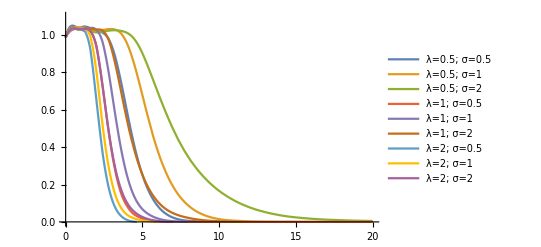

```mathematica
Plot[s,{t, 0, tf}, PlotRange->{0,1.1}, PlotLegends->legend]
```

## Get first-passage time probability

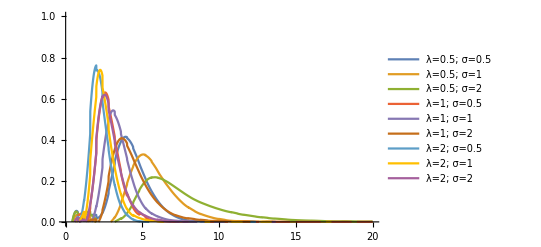

```mathematica
Plot[f,{t, 0, tf}, PlotRange->{0, 1} , PlotLegends->legend]
```

```mathematica
norms = Table[NIntegrate[fp, {t, 0, tf}], {fp, f}]
means = Table[NIntegrate[fp*t, {t, 0, tf}], {fp, f}]
second = Table[NIntegrate[fp*t*t, {t, 0, tf}], {fp, f}]
vars = second-means^2
```

{0.98711,0.987072,0.982325,0.987108,0.987108,0.987137,0.987108,0.987108,0.987108}

{4.48585,5.96074,7.70645,2.95819,3.60257,4.49297,2.34575,2.61376,2.9984}

{20.6851,36.8381,65.2254,9.12978,13.4432,21.2831,5.68479,7.12142,9.4192}

{0.562282,1.30762,5.83604,0.378864,0.46469,1.0963,0.18223,0.28966,0.42879}

```mathematica
λs = { 0.5, 1, 2};
σs = {0.5, 1, 2};
grid = Flatten[Table[{l, s}, {l, λs}, {s, σs}], 1];
v = Table[{va}, {va, vars}];
```

```mathematica
varArray = ArrayReshape[vars, {3, 3}]
```

{{0.562282,1.30762,5.83604},{0.378864,0.46469,1.0963},{0.18223,0.28966,0.42879}}

```mathematica
data = MapThread[Join, {grid, v}]
```

{{0.5,0.5,0.562282},{0.5,1,1.30762},{0.5,2,5.83604},{1,0.5,0.378864},{1,1,0.46469},{1,2,1.0963},{2,0.5,0.18223},{2,1,0.28966},{2,2,0.42879}}

```mathematica
xticks = Table[ToString[i], {i, λs}]
yticks = Table[ToString[i], {i, σs}]
```

{0.5,1,2}

{0.5,1,2}

```mathematica
ArrayPlot[varArray, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->Automatic]
```

-Graphics-